## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
lambdamin=400; (*nm*)
lambdamax=700;(*nm*)
radiomin=10; (*nm*)
radiomax=100; (*nm*)
refractiveindexAire=1;
refractiveindexAgua=1.33;
energyTicksMajor={1.8,1.9,2.1,2.3,2.5,2.8,3.1};
energyTicksMinor={3.5,4.2,4.6,6,8,9,12,40};
radios=Range[10,100,22];
lambdas=Range[lambdamin,lambdamax,10];
refractiveindexes=Range[1,2,0.01];
```

El programa de a continuación está diseñado para ingresar arreglos de datos experimentales

```mathematica
(*Se definen las funciones de Riccati-Bessel y sus correspondientes diferenciales *)
```

```mathematica
ψn[n_,x_]:= x*SphericalBesselJ[n,x]
ξn[n_,x_]:=x*SphericalHankelH1[n,x]
dψn[n_,x_]:=-n *SphericalBesselJ[n,x]+ x * SphericalBesselJ[n-1,x] 
dξn[n_,x_]:=-n * SphericalHankelH1[n,x] + x* SphericalHankelH1[n-1,x]
```

### Definición de funciones

```mathematica
(* Se define el criterio de Wiscombe y se emplea la siguiente notación:
- nm -> Índice de refracción del medio en el que está inmersa la nanopartícula
- a -> Radio de la nanopartícula
- lambda -> Longitud de onda de interés
- n -> multipolo a considerar
*)
```

```mathematica
criterioWiscombe[nm_,a_,lambda_]:=Module[{x,Wiscombe},
						x=(2 Pi nm a)/lambda;							
						Wiscombe=Round[x+ 4*x^(1/3)+2];
						Wiscombe]
```

```mathematica
(* Se definen los coeficientes de Mie y se emplea la siguiente notación:
- np -> Índice de refracción de la nanopartícula
- nm -> Índice de refracción del medio en el que está inmersa la nanopartícula
- a -> Radio de la nanopartícula
- lambda -> Longitud de onda de interés
- n -> multipolo a considerar
*)
```

```mathematica
mieCoefAn[np_,nm_,a_,lambda_,n_]:=Module[{m,x,an},
						m=np/nm;
						x=(2 Pi nm a)/lambda;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
mieCoefBn[np_,nm_,a_,lambda_,n_]:=Module[{m,x,bn},
						m=np/nm;
						x=(2 Pi nm a)/lambda;							
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

```mathematica
(* Se definen las secciones transversales de esparcimiento, absorción y extinción con la siguiente notación
- np -> Índice de refracción de la nanopartícula
- nm -> Índice de refracción del medio en el que está inmersa la nanopartícula
- a -> Radio de la nanopartícula
- lambda -> Longitud de onda de interés
- nmax -> Sumar las contribucion es desde el dipolo hasta el nmax multipolo
Estas funciones regresan cuatro valores en su salida en el orden:
- an -> Modo eléctrico
- bn -> Modo magnético
- Csca/Cabs/Cext -> Sección transversal de esparcimiento/absorción/extinción
- Qsca/Qabs/Qext -> Eficiencia de esparcimiento/absorción/extinción
*)
```

```mathematica
mieQsca[np_,nm_,a_,lambda_]:=Module[{nmax,an,bn,k,Csca,Qsca},
nmax=criterioWiscombe[nm,a,lambda];
an=mieCoefAn[np,nm,a,lambda,#]&/@Range[1,nmax];
bn=mieCoefBn[np,nm,a,lambda,#]&/@Range[1,nmax];
Csca= (lambda^2 )/(2*π* Norm[nm]^2)*(Sum[(2 n +1)(Norm[an[[n]] ]^2+Norm[bn[[n]]] ^2),{n,nmax}]);
Qsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca}]
```

```mathematica
mieQext[np_,nm_,a_,lambda_]:=Module[{nmax,an,bn,Cext,Qext},
nmax=criterioWiscombe[nm,a,lambda];
an=mieCoefAn[np,nm,a,lambda,#]&/@Range[1,nmax];
bn=mieCoefBn[np,nm,a,lambda,#]&/@Range[1,nmax];
Cext=(lambda^2)/(2 Pi Norm[nm]^2)*Sum[(2 n+1) (Re[an[[n]]]+Re[bn[[n]]]),{n,1,nmax}];
Qext=Cext/(Pi a^2);
{an,bn,Cext,Qext}]
```

```mathematica
mieQabs[np_,nm_,a_,lambda_]:=mieQext[np,nm,a,lambda]-mieQsca[np,nm,a,lambda]
```

```mathematica
(* Función para graficar las 3 eficiencias con un solo radio*)
```

```mathematica
plotMieEfficiencies[qext_,qsca_,qabs_,energyTicksMajor_,radius_,lambdamin_,lambdamax_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)ListLinePlot[{qext,Style[qsca,Dashed,Red],qabs},Frame->True,FrameStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],FrameLabel->{{Row[Style[#,Magnification->1.6]&/@{Subscript["Q","ext"],Subscript["Q","abs"],Subscript["Q","sca"]},","],None},{Style["λ [nm]",Magnification->1.6],Style["ℏω [eV]",Magnification->1.6]}},LabelStyle->{FontFamily->"Arial",Black},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,PlotLegends->Placed[SwatchLegend[{Style[Subscript["Q","ext"],Magnification->1.1],Style[Subscript["Q","sca"],Magnification->1.1],Style[Subscript["Q","abs"],Magnification->1.1]},LegendMarkerSize->{15,5},LegendMargins->0,LegendLayout->{"Column",1}],{0.85,0.75}],ImagePadding->{{70,10},{50,50}},PlotLabel->Style[Row[{"Radio ",radius," nm"}],FontFamily->"Arial",Magnification->1.5]]];
```

```mathematica
(* Función para graficar una eficiencia pero con varios radios*)
```

```mathematica
plotMieEfficiencie[qlist_,energyTicksMajor_,lambdamin_,lambdamax_,radios_]:=Module[{majorTicks},(*Calcular ticks mayores en energía*)majorTicks=Module[{positions},positions=h c/#&/@energyTicksMajor;
Transpose[{positions,energyTicksMajor}]];
(*Graficar*)ListLinePlot[qlist,Frame->True,FrameStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],FrameLabel->{{Row[Style[#,Magnification->1.6]&/@{Subscript["Q","ext"]}],None},{Style["λ [nm]",Magnification->1.6],Style["ℏω [eV]",Magnification->1.6]}},LabelStyle->{FontFamily->"Arial",Black},FrameTicks->{{Automatic,None},{Automatic,majorTicks}},PlotRange->All,PlotLegends->Placed[LineLegend[Table[Style["r = "<>ToString[r]<>" nm",Magnification->1.1],{r,radios}],LegendMarkerSize->{15,5},LegendMargins->0,LegendLayout->{"Column",1}],{0.85,0.55}],ImagePadding->{{70,10},{50,50}}
]
]
```

```mathematica
(* Función para hacer un mapa de intensidades de Qsca variando radio y longitud de onda*)
```

```mathematica
plotQDensity[qsca_]:=
ListDensityPlot[qsca,FrameLabel->{"λ [nm]","a [nm]"},ColorFunction->"SunsetColors",InterpolationOrder->1,Mesh->Automatic,Frame->True,FrameStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],ImagePadding->{{70,10},{50,30}},PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],LegendLabel->Subscript["Q","sca"],LegendMarkerSize->200],{After,Top}]]
```

```mathematica
(* Función para hacer un mapa de intensidades de Qsca variando índice de refracción y longitud de onda*)
```

```mathematica
plotQDensityRI[qsca_]:=
ListDensityPlot[qsca,FrameLabel->{"λ [nm]"," RI"},ColorFunction->"SunsetColors",InterpolationOrder->1,Mesh->Automatic,Frame->True,FrameStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],ImagePadding->{{70,10},{50,30}},PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Black,FontFamily->"Arial",Magnification->1.4],LegendLabel->Subscript["Q","sca"],LegendMarkerSize->200],{After,Top}]]
```

```mathematica
(* Función para hacer un mapa de intensidades de Qsca variando índice de refracción, longitud de onda y radio*)
```

```mathematica
plotQDensityRI3D[qsca_]:=
ListDensityPlot3D[qsca,ColorFunction->"SunsetColors",ImagePadding->{{70,10},{50,30}},PlotLegends->Automatic,PlotRange->All]
```

## Vidrio

```mathematica
gCabsMie=Table[{λ,mieQabs[1.5,1.33,4000,λ][[3]]},{λ,400,1000,5}];
gCscaMie=Table[{λ,mieQsca[1.5,1.33,4000,λ][[3]]},{λ,400,1000,5}];
gCextMie=Table[{λ,mieQext[1.5,1.33,4000,λ][[3]]},{λ,400,1000,5}];
```

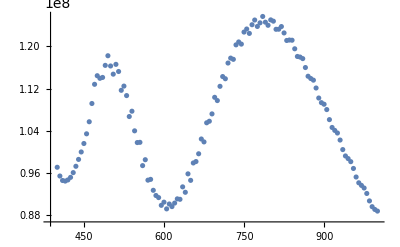

```mathematica
ListPlot[{gCextMie}]
```

```mathematica
mieQext[1.5,1.33,4000,435][[3]]
```

9.72699×10^7

```mathematica
h c/1
```

1240.7

```mathematica
1.5^2
```

2.25

```mathematica
1.33^2
```

1.7689

```mathematica
h c/435
```

2.85218

```mathematica
gCextMie
```

{{400,4.38169×10^8},{405,4.3785×10^8},{410,4.30226×10^8},{415,4.21581×10^8},{420,4.11406×10^8},{425,4.01709×10^8},{430,3.94465×10^8},{435,3.91115×10^8},{440,3.92587×10^8},{445,3.99484×10^8},{450,4.12176×10^8},{455,4.21317×10^8},{460,4.27058×10^8},{465,4.35348×10^8},{470,4.43883×10^8},{475,4.40009×10^8},{480,4.42303×10^8},{485,4.33669×10^8},{490,4.25972×10^8},{495,4.18225×10^8},{500,4.0904×10^8},{505,3.99547×10^8},{510,4.02625×10^8},{515,3.89177×10^8},{520,3.90923×10^8},{525,3.94121×10^8},{530,3.94925×10^8},{535,4.02836×10^8},{540,4.16931×10^8},{545,4.19826×10^8},{550,4.25857×10^8},{555,4.3921×10^8},{560,4.40887×10^8},{565,4.49223×10^8},{570,4.49702×10^8},{575,4.49978×10^8},{580,4.47972×10^8},{585,4.44235×10^8},{590,4.3927×10^8},{595,4.33484×10^8},{600,4.27139×10^8},{605,4.20238×10^8},{610,4.12857×10^8},{615,4.05565×10^8},{620,3.99103×10^8},{625,3.93882×10^8},{630,3.89923×10^8},{635,3.87179×10^8},{640,3.85675×10^8},{645,3.86042×10^8},{650,3.94246×10^8},{655,3.90879×10^8},{660,4.01781×10^8},{665,4.00559×10^8},{670,4.05432×10^8},{675,4.11507×10^8},{680,4.23114×10^8},{685,4.31337×10^8},{690,4.32423×10^8},{695,4.37016×10^8},{700,4.48986×10^8}}

Datos obtenidos de Johnson & Christy  DOI: https://doi.org/10.1103/PhysRevB.6.4370

```mathematica
au=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en nm*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
aU=Transpose[{λAu,nAu}];
```

```mathematica
nindexau=Interpolation[aU];
```

```mathematica
auCabsMie=Table[{λ,mieQabs[nindexau[λ],1,30,λ][[3]]},{λ,250,1000,5}];
auCscaMie=Table[{λ,mieQsca[nindexau[λ],1,30,λ][[3]]},{λ,250,1000,5}];
auCextMie=Table[{λ,mieQext[nindexau[λ],1,30,λ][[3]]},{λ,250,1000,5}];
```

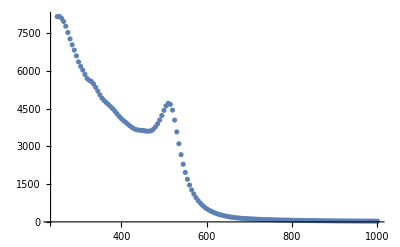

```mathematica
ListPlot[auCextMie]
```

```mathematica
mieQext[nindexau[h c/1.721],1,30,h c/1.721][[3]]
```

104.302

```mathematica
h c/5
```

248.14

```mathematica
upperTicks4=Module[{labels,positions},labels={1.2,1.5,2,3,6};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={1,1.3,1.7,1.8,2.3,2.7,4,5,5.7};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

```mathematica
au1=ListLinePlot[{Style[varindep20,RGBColor[1,0.902,0.145]],Style[varindep21,Orange]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext, Qsca",Black,12],None},{Style["λ [nm]",Black,12],Style["ℏω [eV]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks4,upperTicksMinor4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"Qext","Qsca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

-Graphics-